# To do:

Exclude cells with bad circularity...round or elongated nuclei seem to be in the 0.8-1 range. 0.44 was a very crunchy cell 
Exclude 2 touching cells from being counted as one

# Function

### MyThresholding

```mathematica
(*fin product*)
MyThresholding1Ch[img_,analysisFolder_]:=Module[{myImg=img},
DynamicModule[{flagCol},

(*checking for saved parameters*)
flagCol=If[FileExistsQ@(analysisFolder<>"_th.dat"),th=<<(analysisFolder<>"_th.dat");ToString@th<>"  Already Saved","Not Yet Determined"];

(*control*)
SetOptions[Manipulator,Appearance->"Open"];
Manipulate[
Column@
{Show[ImageAdjust[img,{0,0,1},{threshold1,threshold2}],ImageSize->300],
"Color Threshold  : "<>flagCol},
{{threshold1,0.01},0,0.4,0.001},{{threshold2,0.1},0,0.4,0.001},
Spacer@10,

Button["Save Threshold",
th={threshold1,threshold2};
flagCol=ToString@th<>"Saved";
th>>analysisFolder<>"_th.dat"],
Spacer@5,
Button["Load Pre-Saved Parameters",
If[ ValueQ@th,{threshold1,threshold2}=th];   ],
ControlPlacement->Left
]
]]
```

# Code

## Import image

```mathematica
folder  = "/Users/ccialek/OneDrive - Colostate/2020_Confocal/20200822_sfGFP-H2B-Lin28a-3pUTR/wt UTR/";
files = FileNames[ "*.tif" ,folder] ;
```

```mathematica
myfile = files[[1]]
```

/Users/ccialek/OneDrive - Colostate/2020_Confocal/20200822_sfGFP-H2B-Lin28a-3pUTR/wt UTR/sfGFP-H2B-lin28a-wt-3pUTR - 0 _XY1598119674_confocal.tif

```mathematica
myimg = Import[ myfile];
(*analysisFolder = "/Users/ccialek/Desktop/TEMP/" ;*)
```

```mathematica
slashloc = StringPosition[myfile,"/"] [[-1, 1]];
analysisFolder =StringTake[ myfile, {1,slashloc} ] <> "_Analysis/" <> StringTake[ myfile, {slashloc+1, -5}  ]
```

/Users/ccialek/OneDrive - Colostate/2020_Confocal/20200822_sfGFP-H2B-Lin28a-3pUTR/wt UTR/_Analysis/sfGFP-H2B-lin28a-wt-3pUTR - 0 _XY1598119674_confocal

## Blur

```mathematica
myimgblur = GaussianFilter[myimg,3] ;
```

## Subtract background from image

```mathematica
(*SET background: *)
bkg = 0.0155;
```

```mathematica
data = myimgblur//ImageData;
temp = Table[ data[[row]]  /. x_/;x<bkg -> 0  , {row,1,Length@data}] ;
myimgbkgsbtrk = Image@temp;
```

## Threshold for binarization

```mathematica
th  = {0.01,0.1} ;
```

```mathematica
MyThresholding1Ch[myimgbkgsbtrk,analysisFolder]  ;
```

## Select usable nuclei

```mathematica
(*Select the nuclei : 
Must be large enough to be a nucleus: 
	100000>#Count>1000
Must be circular enough, not some crazy squiggley shape: 
	 #Elongation<.45       <-- don't use this!!! Bad@ 
Must NOT be touching an edge, so we can measure the whole nucleus:
	#AdjacentBorderCount==0 
*)
```

```mathematica
mynucleiimg = SelectComponents[ myimgbkgsbtrk,  600000>#Count>2000&& (*#Elongation<.9   &&*) #AdjacentBorderCount==0&] ;
GraphicsRow[ ImageAdjust[ # , {0.0,1},th]   &/@ {myimgbkgsbtrk,mynucleiimg} , ImageSize->1000 ]
```

-Graphics-

```mathematica
edgecells =  MorphologicalComponents[SelectComponents[ myimgbkgsbtrk,  100000>#Count>1000&& (*#Elongation<.45   && *)#AdjacentBorderCount==1&]  ]// Colorize  ;
```

```mathematica
GraphicsRow[{   myimgblur// ImageAdjust[#,{0,0,1},th]&  ,
   mynucleiimg// ImageAdjust[#,{0,0,1},th]&, 
 MorphologicalComponents[mynucleiimg]//Colorize  , 
edgecells },
 ImageSize->{1000}, Spacings->0]
```

-Graphics-

## Measure nuclei

```mathematica
(*a circularity of less than ~0.7 is a crunchy, shitty nucleus. I should exclude these*)
```

```mathematica
measurments = {"Count","Circularity","TotalIntensity","MeanIntensity", "MaxIntensity" , "IntensityCentroid"} ; myimgmeasurement = ComponentMeasurements[mynucleiimg,measurments] //#[[All,2]]& (*this bit gets rid of {1-> ...} *) ;
myimgmeasurement//TableForm
```

4503 | 0.909595 | 70.1255 | 0.0155731 | 0.0156863 | 442.221
741.168
12417 | 0.849535 | 490.086 | 0.039469 | 0.203922 | 63.9903
552.448
16041 | 0.864666 | 1132.64 | 0.070609 | 0.4 | 244.649
522.481
5603 | 0.886622 | 262.196 | 0.0467957 | 0.196078 | 55.4272
446.084
2470 | 0.911247 | 44.9608 | 0.0182027 | 0.0313725 | 539.147
342.332
3565 | 0.828471 | 56.8196 | 0.0159382 | 0.0196078 | 113.948
319.651
12203 | 0.853598 | 315.875 | 0.025885 | 0.211765 | 345.429
262.929
3113 | 0.743651 | 48.4745 | 0.0155716 | 0.0156863 | 98.797
223.232

```mathematica
myimgmeasurement>>(analysisFolder <> "imgmeasurements.m")
(analysisFolder <> "imgmeasurements.m")
```

/Users/ccialek/OneDrive - Colostate/2020_Confocal/20200822_sfGFP-H2B-Lin28a-3pUTR/wt UTR/_Analysis/sfGFP-H2B-lin28a-wt-3pUTR - 0 _XY1598119674_confocalimgmeasurements.m

# Global

## Import

```mathematica
folderMUT = "/Users/ccialek/OneDrive - Colostate/2020_Confocal/20200822_sfGFP-H2B-Lin28a-3pUTR/mut UTR/" ;
folderWT = "/Users/ccialek/OneDrive - Colostate/2020_Confocal/20200822_sfGFP-H2B-Lin28a-3pUTR/wt UTR/";
```

```mathematica
filesMUT = FileNames[folderMUT<>"_Analysis/*.m" ] ;
filesWT = FileNames[folderWT<>"_Analysis/*.m" ] ;
Length/@{filesMUT,filesWT}
```

{25,23}

```mathematica
myimgmeasurementMUT =  <<(#)&/@filesMUT ;
myimgmeasurementWT =  <<(#)&/@filesWT ;
```

## Plot nuclei intensities

```mathematica
measurments[[4]]
```

MeanIntensity

### Subtract the background

Area * bkg is the value to subtract from total intensity

```mathematica
bkg
```

0.0155

```mathematica
measurments[[4]]
```

MeanIntensity

```mathematica
myTotIntsBkgdSbtkMUT  = Table[
 myimgmeasurementMUT [[cell,All,3]]  -  myimgmeasurementMUT [[cell,All,1]]*bkg , {cell,1,Length@myimgmeasurementMUT}]  ;
myTotIntsBkgdSbtkWT  =Table[
 myimgmeasurementWT [[cell,All,3]]  -  myimgmeasurementWT [[cell,All,1]]*bkg , {cell,1,Length@myimgmeasurementWT}] ;
```

```mathematica
myMeanIntsBkgdSbtkMUT  = Table[ myimgmeasurementMUT [[cell,All,4]]   -  bkg, {cell,1,Length@myimgmeasurementMUT}]  ;
myMeanIntsBkgdSbtkWT  = Table[ myimgmeasurementWT [[cell,All,4]]   - bkg, {cell,1,Length@myimgmeasurementWT}]  ;
```

#### All cells together

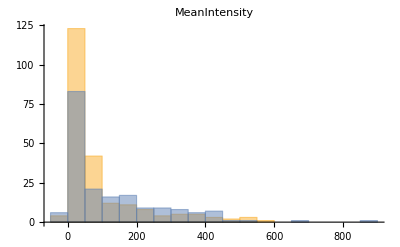

```mathematica
Histogram[Flatten/@{ myTotIntsBkgdSbtkMUT , myTotIntsBkgdSbtkWT} ,PlotLabel-> measurments[[4]]]
```

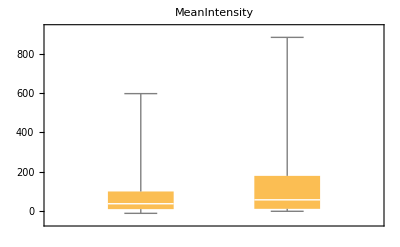

```mathematica
BoxWhiskerChart[Flatten/@{ myTotIntsBkgdSbtkMUT , myTotIntsBkgdSbtkWT} ,PlotLabel-> measurments[[4]]]
```

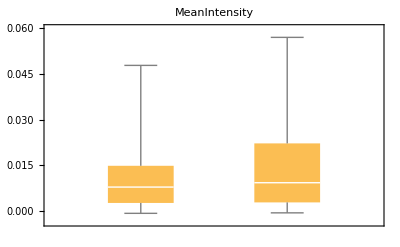

```mathematica
BoxWhiskerChart[Flatten/@{myMeanIntsBkgdSbtkMUT  ,myMeanIntsBkgdSbtkWT } ,PlotLabel-> measurments[[4]]]
```

#### Each image separately

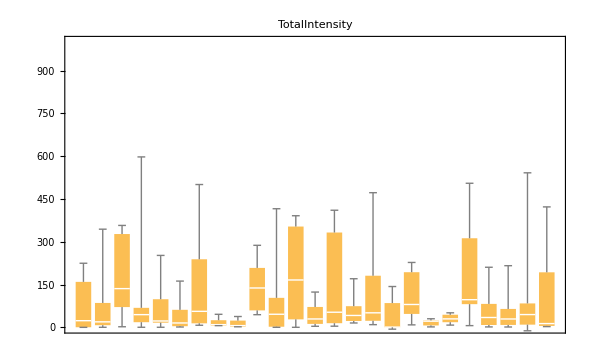

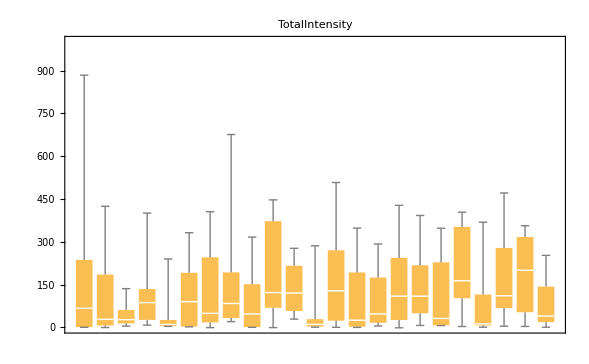

```mathematica
BoxWhiskerChart[myTotIntsBkgdSbtkMUT ,PlotLabel-> measurments[[3]],PlotRange->{{All,All},{0,1000}}]
BoxWhiskerChart[myTotIntsBkgdSbtkWT  ,PlotLabel-> measurments[[3]],PlotRange->{{All,All},{0,1000}}]
```